## Setup

```mathematica
wd =SetDirectory@NotebookDirectory[]
```

/home/stricklandlab/Desktop/quenching_cuba_integration/mathematica

```mathematica
SetOptions[{Plot,ListPlot,LogPlot,ListLogPlot,LogLinearPlot,Histogram,DensityHistogram,ListStepPlot},Frame->True,Axes->False,ImageSize->450,AspectRatio->0.7,BaseStyle->18,FrameStyle->AbsoluteThickness[1]];
```

```mathematica
myLog[x_]:={x[[1]],x[[2]],Log[x[[3]]]}
```

```mathematica
plotColor1= ColorData[97,"ColorList"][[1]];
plotColor2= ColorData[97,"ColorList"][[2]];
plotColor3= ColorData[97,"ColorList"][[3]];
plotColor4= ColorData[97,"ColorList"][[4]];
plotColor5= ColorData[97,"ColorList"][[5]];
```

## Load params

```mathematica
my1SParams=StringSplit/@Select[Select[StringSplit[Import[wd<>"/../output_1S/params.txt"],"\n"],!StringStartsQ[#, "//"]&] ,StringLength[#]>0&]
my2SParams=StringSplit/@Select[Select[StringSplit[Import[wd<>"/../output_2S/params.txt"],"\n"],!StringStartsQ[#, "//"]&] ,StringLength[#]>0&]
my3SParams=StringSplit/@Select[Select[StringSplit[Import[wd<>"/../output_3S/params.txt"],"\n"],!StringStartsQ[#, "//"]&] ,StringLength[#]>0&]
myJPsiParams=StringSplit/@Select[Select[StringSplit[Import[wd<>"/../output_JPsi/params.txt"],"\n"],!StringStartsQ[#, "//"]&] ,StringLength[#]>0&]
myDict=Association[Table[myParams[[i,1]]->ToExpression[myParams[[i,2]]],{i,1,Length[myParams]}]];
```

{{collisionType,0},{nc,3},{alphas,0},{massQQ,9.460},{lambdaQCD,0.308},{qhat0,0.075},{lp,1.5},{lA,10.11},{lB,10.11},{massp,0.938},{rootsnn,5023},{Ny,21},{Npt,81},{y_min,-5.0},{y_max,5.0},{ptmin,0.1},{ptmax,40.1}}

{{collisionType,0},{nc,3},{alphas,0},{massQQ,10.02326},{lambdaQCD,0.308},{qhat0,0.075},{lp,1.5},{lA,10.11},{lB,10.11},{massp,0.938},{rootsnn,5023},{Ny,21},{Npt,81},{y_min,-5.0},{y_max,5.0},{ptmin,0.1},{ptmax,40.1}}

{{collisionType,0},{nc,3},{alphas,0},{massQQ,10.3552},{lambdaQCD,0.308},{qhat0,0.075},{lp,1.5},{lA,10.11},{lB,10.11},{massp,0.938},{rootsnn,5023},{Ny,21},{Npt,81},{y_min,-5.0},{y_max,5.0},{ptmin,0.1},{ptmax,40.1}}

{{collisionType,0},{nc,3},{alphas,0},{massQQ,3.0969},{lambdaQCD,0.308},{qhat0,0.075},{lp,1.5},{lA,10.11},{lB,10.11},{massp,0.938},{rootsnn,5023},{Ny,21},{Npt,81},{y_min,-5.0},{y_max,5.0},{ptmin,0.1},{ptmax,40.1}}

```mathematica
(* load variables from params file to automate some things below *)
M = myDict["massQQ"]
roots = myDict["rootsnn"]
```

Missing[KeyAbsent,massQQ]

Missing[KeyAbsent,rootsnn]

```mathematica
Missing["KeyAbsent","massQQ"]
```

Missing[KeyAbsent,massQQ]

## General functions

```mathematica
Mperp2[pt_] = pt^2+M^2; (* GeV ^2 *)
Mperp[pt_] = Sqrt[Mperp2[pt]]; (* GeV *)
ymaxFunction[pt_] = Log[roots/Mperp[pt]];
ptmaxFunction[y_]=Sqrt[(roots Exp[-y])^2 - M^2];
```

```mathematica
Grid[{{Plot[ymaxFunction[pt],{pt,0,50},FrameLabel->{"p_T [GeV]","ymax"}],Plot[ptmaxFunction[y],{y,0,5},FrameLabel->{"y","p_(T, max) [GeV]"}]}}]
```

-Graphics- | -Graphics-

## Read pA data

```mathematica
pA1SresultLog=Interpolation[myLog/@Import[wd<>"/../output_1S/pA-cross-section.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic];
pA1SerrorLog=Interpolation[myLog/@Import[wd<>"/../output_1S/pA-cross-section.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic];
{ymin,ymax} = pAresultLog[[1,1]]
{ptmin,ptmax} = pAresultLog[[1,2]]
pA1Sresult[y_,pt_]:=Exp[pA1SresultLog[y,pt]]
pA1Serror[y_,pt_]:=Exp[pA1SerrorLog[y,pt]]
```

Part::partd: Part specification pAresultLog⟦1,1⟧ is longer than depth of object.

Set::shape: Lists {ymin,ymax} and pAresultLog⟦1,1⟧ are not the same shape.

pAresultLog⟦1,1⟧

Part::partd: Part specification pAresultLog⟦1,2⟧ is longer than depth of object.

Set::shape: Lists {ptmin,ptmax} and pAresultLog⟦1,2⟧ are not the same shape.

pAresultLog⟦1,2⟧

```mathematica
pA2SresultLog=Interpolation[myLog/@Import[wd<>"/../output_2S/pA-cross-section.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic];
pA2SerrorLog=Interpolation[myLog/@Import[wd<>"/../output_2S/pA-cross-section.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic];
{ymin,ymax} = pA2SresultLog[[1,1]]
{ptmin,ptmax} = pA2SresultLog[[1,2]]
pA2Sresult[y_,pt_]:=Exp[pA2SresultLog[y,pt]]
pA2Serror[y_,pt_]:=Exp[pA2SerrorLog[y,pt]]
```

{-5.,5.}

{0.1,40.1}

```mathematica
pA3SresultLog=Interpolation[myLog/@Import[wd<>"/../output_3S/pA-cross-section.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic];
pA3SerrorLog=Interpolation[myLog/@Import[wd<>"/../output_3S/pA-cross-section.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic];
{ymin,ymax} = pA3SresultLog[[1,1]]
{ptmin,ptmax} = pA3SresultLog[[1,2]]
pA3Sresult[y_,pt_]:=Exp[pA3SresultLog[y,pt]]
pA3Serror[y_,pt_]:=Exp[pA3SerrorLog[y,pt]]
```

{-5.,5.}

{0.1,40.1}

```mathematica
pAJPsiresultLog=Interpolation[myLog/@Import[wd<>"/../output_JPsi/pA-cross-section.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic];
pAJPsierrorLog=Interpolation[myLog/@Import[wd<>"/../output_JPsi/pA-cross-section.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic];
{ymin,ymax} = pAJPsiresultLog[[1,1]]
{ptmin,ptmax} = pAJPsiresultLog[[1,2]]
pAJPsiresult[y_,pt_]:=Exp[pAJPsiresultLog[y,pt]]
pAJPsierror[y_,pt_]:=Exp[pAJPsierrorLog[y,pt]]
```

{-5.,5.}

{0.1,40.1}

```mathematica
Plot3D[pA1Sresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
Plot3D[pA1Serror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

-Graphics3D-

```mathematica
Plot3D[pA2Sresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
Plot3D[pA2Serror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

-Graphics3D-

```mathematica
Plot3D[pA3Sresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
Plot3D[pA3Serror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

-Graphics3D-

```mathematica
Plot3D[pAJPsiresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
Plot3D[pAJPsierror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

-Graphics3D-

## Read AB data

```mathematica
ABresultLog=Interpolation[myLog/@Import[wd<>"/../output/AB-cross-section.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic];
ABerrorLog=Interpolation[myLog/@Import[wd<>"/../output/AB-cross-section.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic];
{ymin,ymax} = ABresultLog[[1,1]]
{ptmin,ptmax} = ABresultLog[[1,2]]
ABresult[y_,pt_]:=Exp[ABresultLog[y,pt]]
ABerror[y_,pt_]:=Exp[ABerrorLog[y,pt]]
```

Import::nffil: File /home/stricklandlab/Desktop/quenching_cuba_integration/mathematica/../output/AB-cross-section.tsv not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Interpolation::innd: First argument in Symbol[] does not contain a list of data and coordinates.

Import::nffil: File /home/stricklandlab/Desktop/quenching_cuba_integration/mathematica/../output/AB-cross-section.tsv not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Interpolation::innd: First argument in Symbol[] does not contain a list of data and coordinates.

Part::partw: Part 1 of Symbol[] does not exist.

Set::shape: Lists {ymin,ymax} and Interpolation[Symbol[],InterpolationOrder→Automatic]⟦1,1⟧ are not the same shape.

Interpolation[Symbol[],InterpolationOrder→Automatic]⟦1,1⟧

Part::partw: Part 2 of Symbol[] does not exist.

Set::shape: Lists {ptmin,ptmax} and Interpolation[Symbol[],InterpolationOrder→Automatic]⟦1,2⟧ are not the same shape.

Interpolation[Symbol[],InterpolationOrder→Automatic]⟦1,2⟧

```mathematica
Plot3D[ABresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

```mathematica
Plot3D[ABerror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

## Read pp data

```mathematica
ppresultLog=Interpolation[myLog/@Import[wd<>"/../output/pp-cross-section.tsv"],InterpolationOrder->Automatic];
ppresult[y_,pt_]:=Exp[ppresultLog[y,pt]]
```

Import::nffil: File /home/stricklandlab/Desktop/quenching_cuba_integration/mathematica/../output/pp-cross-section.tsv not found during Import.

Interpolation::innd: First argument in $Failed does not contain a list of data and coordinates.

```mathematica
Plot3D[ppresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

## Read RAB data

```mathematica
RABresult=Interpolation[Import[wd<>"/../output_1S/RAB.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic]
RABerror=Interpolation[Import[wd<>"/../output_1S/RAB.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic]
{ymin,ymax} = RABresult[[1,1]];
{ptmin,ptmax} =RABresult[[1,2]];
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
Plot3D[RABresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->{0,1.5}]
```

-Graphics3D-

```mathematica
(*Plot3D[RABerror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->Automatic]*)
```

```mathematica
RABresultU[y_,pt_]=RABresult[y,pt]+RABerror[y,pt];
RABresultL[y_,pt_]=RABresult[y,pt]-RABerror[y,pt];
```

```mathematica
myPlotY[pt_]:=Plot[{RABresult[y,pt],RABresultL[y,pt],RABresultU[y,pt]},{y,ymin,ymax},PlotStyle->{plotColor1,{Opacity[0.1],plotColor1},{Opacity[0.1],plotColor1}},Filling->{2->{3}},PlotLabel->Style["p_T = "<>ToString[pt]<>" GeV",18],FrameLabel->{"y","R_AB"},ImageSize->400,PlotRange->{0,1.5}]
myPlotPT[y_]:=Plot[{RABresult[y,pt],RABresultL[y,pt],RABresultU[y,pt]},{pt,ptmin,ptmax},PlotStyle->{plotColor1,{Opacity[0.1],plotColor1},{Opacity[0.1],plotColor1}},Filling->{2->{3}},PlotLabel->Style["y = "<>ToString[y],18],FrameLabel->{"p_T [GeV]","R_AB"},ImageSize->400,PlotRange->{0,1.5}]
```

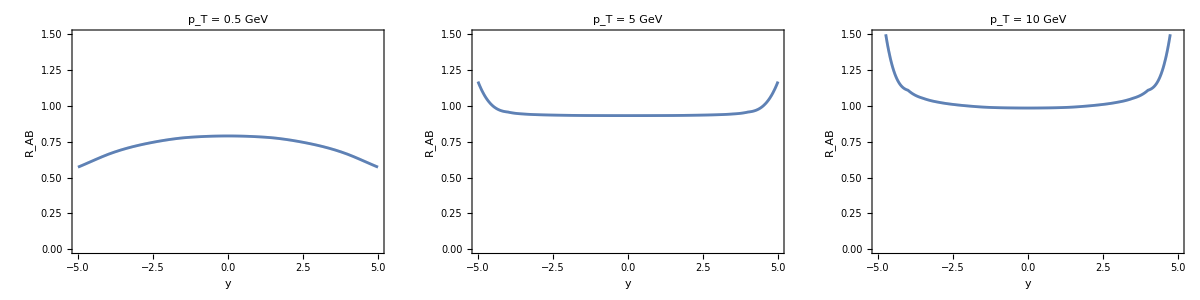

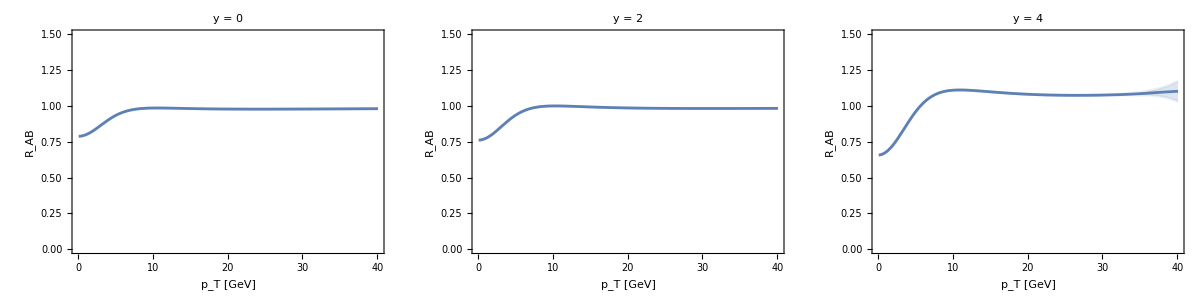

```mathematica
Grid[{{myPlotY[0.5],myPlotY[5],myPlotY[10]}}]
Grid[{{myPlotPT[0],myPlotPT[2],myPlotPT[4]}}]
```

## Read RpA data Υ(Avg)

```mathematica
RpAYresult=Interpolation[Import[wd<>"/../output_Avg_NewLeff/RpA.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic]
RpAYerror=Interpolation[Import[wd<>"/../output_Avg_NewLeff/RpA.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic]
{ymin,ymax} =RpAYresult[[1,1]];
{ptmin,ptmax} =RpAYresult[[1,2]];
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
Plot3D[RpAYresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->{0,1.5}]
```

-Graphics3D-

```mathematica
(*Plot3D[RpAerror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->Automatic]*)
```

```mathematica
RpAYresultU[y_,pt_]=RpAYresult[y,pt]+RpAYerror[y,pt];
RpAYresultL[y_,pt_]=RpAYresult[y,pt]-RpAYerror[y,pt];
```

```mathematica
mypAYPlotY[pt_]:=Plot[{RpAYresult[y,pt],RpAYresultL[y,pt],RpAYresultU[y,pt]},{y,ymin,ymax},PlotStyle->{Red,{Opacity[0.1],Red},{Opacity[0.1],Red}},Filling->{2->{3}},PlotLabel->Style["p_T = "<>ToString[pt]<>" GeV",18],FrameLabel->{"y","R_pA"},ImageSize->400,PlotRange->{0,1.5},PlotLegends->Placed[{"Υ"},{Right,Bottom}]]
mypAYPlotPT[y_]:=Plot[{RpAYresult[y,pt],RpAYresultL[y,pt],RpAYresultU[y,pt]},{pt,ptmin,ptmax},PlotStyle->{Red,{Opacity[0.1],Red},{Opacity[0.1],Red}},Filling->{2->{3}},PlotLabel->Style["y = "<>ToString[y],18],FrameLabel->{"p_T [GeV]","R_pA"},ImageSize->400,PlotRange->{0,1.5},PlotLegends->Placed[{"Υ"},{Right,Bottom}]]
```

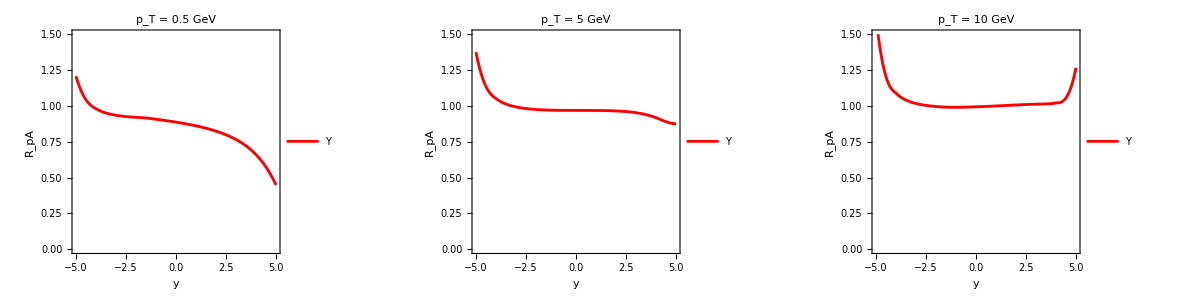

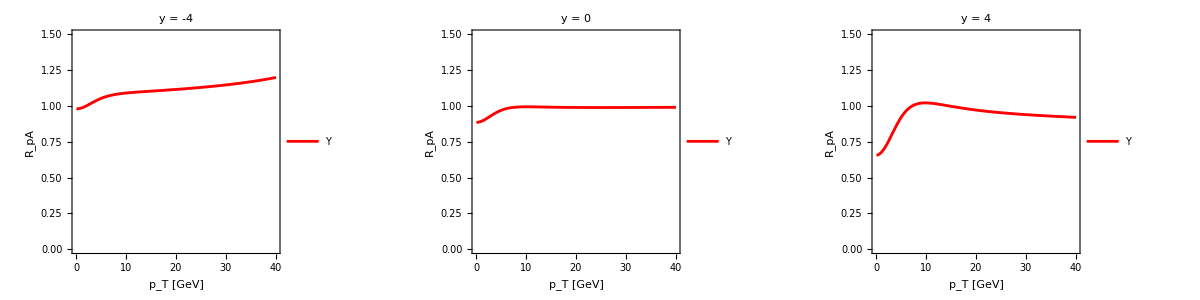

```mathematica
plot0=Grid[{{mypAYPlotY[0.5],mypAYPlotY[5],mypAYPlotY[10]}}]
plot01=Grid[{{mypAYPlotPT[-4],mypAYPlotPT[0],mypAYPlotPT[4]}}]
```

## Read RpA data Υ(1S)

```mathematica
RpA1Sresult=Interpolation[Import[wd<>"/../archive/output_Yavg/RpA.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic]
RpA1Serror=Interpolation[Import[wd<>"/../archive/output_Yavg/RpA.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic]
{ymin,ymax} =RpA1Sresult[[1,1]];
{ptmin,ptmax} =RpA1Sresult[[1,2]];
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
Plot3D[RpA1Sresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->{0,1.5}]
```

-Graphics3D-

```mathematica
(*Plot3D[RpAerror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->Automatic]*)
```

```mathematica
RpA1SresultU[y_,pt_]=RpA1Sresult[y,pt]+RpA1Serror[y,pt];
RpA1SresultL[y_,pt_]=RpA1Sresult[y,pt]-RpA1Serror[y,pt];
```

```mathematica
mypA1SPlotY[pt_]:=Plot[{RpA1Sresult[y,pt],RpA1SresultL[y,pt],RpA1SresultU[y,pt]},{y,ymin,ymax},PlotStyle->{plotColor1,{Opacity[0.1],plotColor1},{Opacity[0.1],plotColor1}},Filling->{2->{3}},PlotLabel->Style["p_T = "<>ToString[pt]<>" GeV",18],FrameLabel->{"y","R_pA"},ImageSize->400,PlotRange->{0,1.5},PlotLegends->Placed[{"Υ(1S)"},{Right,Bottom}]]
mypA1SPlotPT[y_]:=Plot[{RpA1Sresult[y,pt],RpA1SresultL[y,pt],RpA1SresultU[y,pt]},{pt,ptmin,ptmax},PlotStyle->{plotColor1,{Opacity[0.1],plotColor1},{Opacity[0.1],plotColor1}},Filling->{2->{3}},PlotLabel->Style["y = "<>ToString[y],18],FrameLabel->{"p_T [GeV]","R_pA"},ImageSize->400,PlotRange->{0,1.5},PlotLegends->Placed[{"Υ(1S)"},{Right,Bottom}]]
```

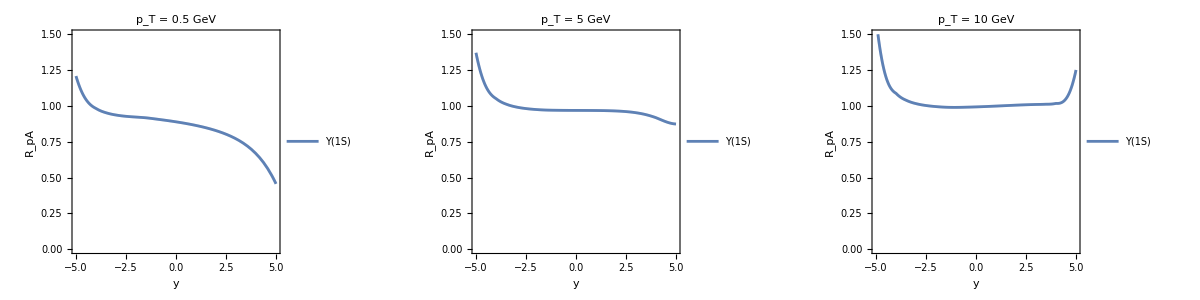

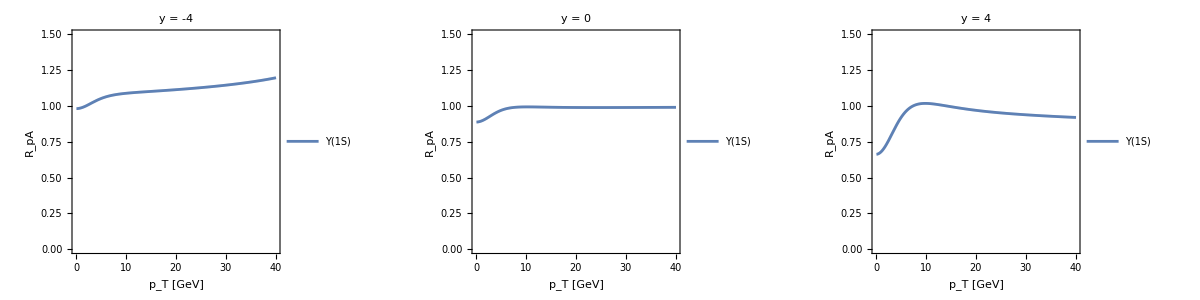

```mathematica
plot1=Grid[{{mypA1SPlotY[0.5],mypA1SPlotY[5],mypA1SPlotY[10]}}]
plot2=Grid[{{mypA1SPlotPT[-4],mypA1SPlotPT[0],mypA1SPlotPT[4]}}]
```

## Read RpA data Υ(2S)

```mathematica
RpA2Sresult=Interpolation[Import[wd<>"/../output_2S/RpA.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic]
RpA2Serror=Interpolation[Import[wd<>"/../output_2S/RpA.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic]
{ymin,ymax} =RpA2Sresult[[1,1]];
{ptmin,ptmax} =RpA2Sresult[[1,2]];
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
Plot3D[RpA2Sresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->{0,1.5}]
```

-Graphics3D-

```mathematica
(*Plot3D[RpAerror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->Automatic]*)
```

```mathematica
RpA2SresultU[y_,pt_]=RpA2Sresult[y,pt]+RpA2Serror[y,pt];
RpA2SresultL[y_,pt_]=RpA2Sresult[y,pt]-RpA2Serror[y,pt];
```

```mathematica
mypA2SPlotY[pt_]:=Plot[{RpA2Sresult[y,pt],RpA2SresultL[y,pt],RpA2SresultU[y,pt]},{y,ymin,ymax},PlotStyle->{plotColor2,{Opacity[0.1],plotColor2},{Opacity[0.1],plotColor2}},Filling->{2->{3}},PlotLabel->Style["p_T = "<>ToString[pt]<>" GeV",18],FrameLabel->{"y","R_pA"},ImageSize->400,PlotRange->{0,1.5},PlotLegends->Placed[{"Υ(2S)"},{Right,Bottom}]]
mypA2SPlotPT[y_]:=Plot[{RpA2Sresult[y,pt],RpA2SresultL[y,pt],RpA2SresultU[y,pt]},{pt,ptmin,ptmax},PlotStyle->{plotColor2,{Opacity[0.1],plotColor2},{Opacity[0.1],plotColor2}},Filling->{2->{3}},PlotLabel->Style["y = "<>ToString[y],18],FrameLabel->{"p_T [GeV]","R_pA"},ImageSize->400,PlotRange->{0,1.5},PlotLegends->Placed[{"Υ(2S)"},{Right,Bottom}]]
```

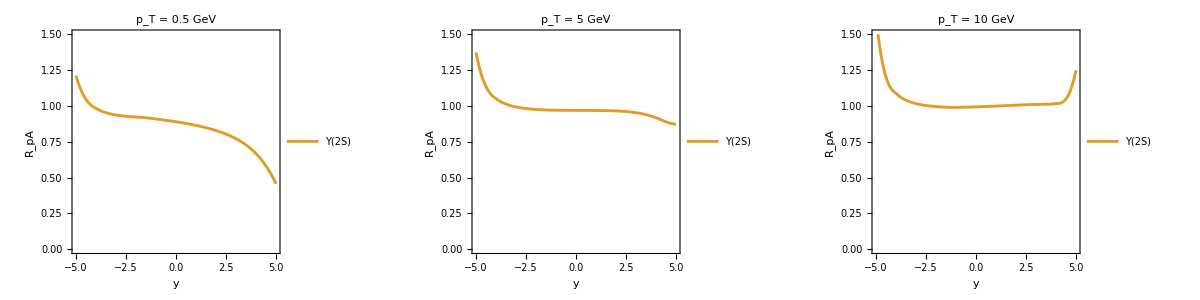

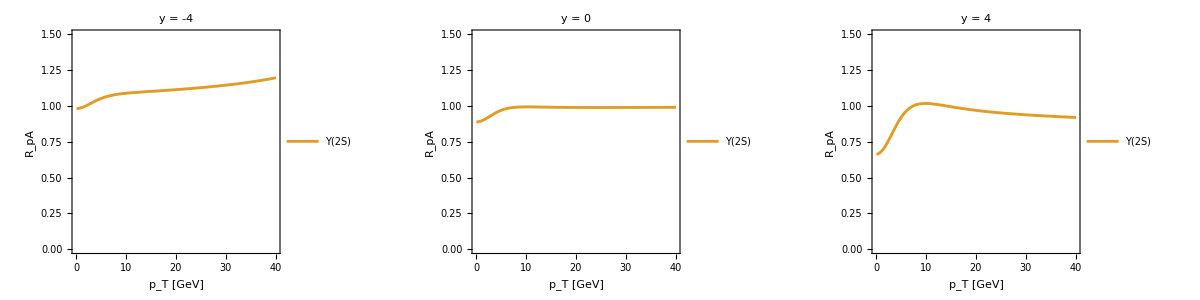

```mathematica
plot3=Grid[{{mypA2SPlotY[0.5],mypA2SPlotY[5],mypA2SPlotY[10]}}]
plot4=Grid[{{mypA2SPlotPT[-4],mypA2SPlotPT[0],mypA2SPlotPT[4]}}]
```

## Read RpA data Υ(3S)

```mathematica
RpA3Sresult=Interpolation[Import[wd<>"/../output_3S/RpA.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic]
RpA3Serror=Interpolation[Import[wd<>"/../output_3S/RpA.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic]
{ymin,ymax} =RpA3Sresult[[1,1]];
{ptmin,ptmax} =RpA3Sresult[[1,2]];
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
Plot3D[RpA3Sresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->{0,1.5}]
```

-Graphics3D-

```mathematica
(*Plot3D[RpAerror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->Automatic]*)
```

```mathematica
RpA3SresultU[y_,pt_]=RpA3Sresult[y,pt]+RpA3Serror[y,pt];
RpA3SresultL[y_,pt_]=RpA3Sresult[y,pt]-RpA3Serror[y,pt];
```

```mathematica
mypA3SPlotY[pt_]:=Plot[{RpA3Sresult[y,pt],RpA3SresultL[y,pt],RpA3SresultU[y,pt]},{y,ymin,ymax},PlotStyle->{plotColor3,{Opacity[0.1],plotColor3},{Opacity[0.1],plotColor3}},Filling->{2->{3}},PlotLabel->Style["p_T = "<>ToString[pt]<>" GeV",18],FrameLabel->{"y","R_pA"},ImageSize->400,PlotRange->{0,1.5},PlotLegends->Placed[{"Υ(3S)"},{Right,Bottom}]]
mypA3SPlotPT[y_]:=Plot[{RpA3Sresult[y,pt],RpA3SresultL[y,pt],RpA3SresultU[y,pt]},{pt,ptmin,ptmax},PlotStyle->{plotColor3,{Opacity[0.1],plotColor3},{Opacity[0.1],plotColor3}},Filling->{2->{3}},PlotLabel->Style["y = "<>ToString[y],18],FrameLabel->{"p_T [GeV]","R_pA"},ImageSize->400,PlotRange->{0,1.5},PlotLegends->Placed[{"Υ(3S)"},{Right,Bottom}]]
```

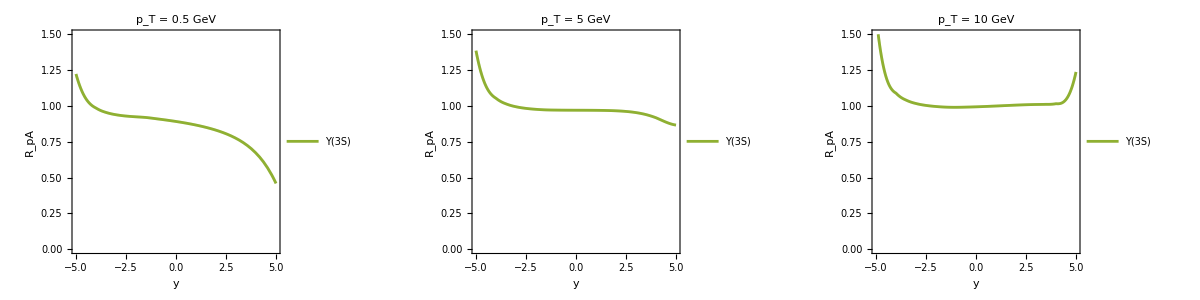

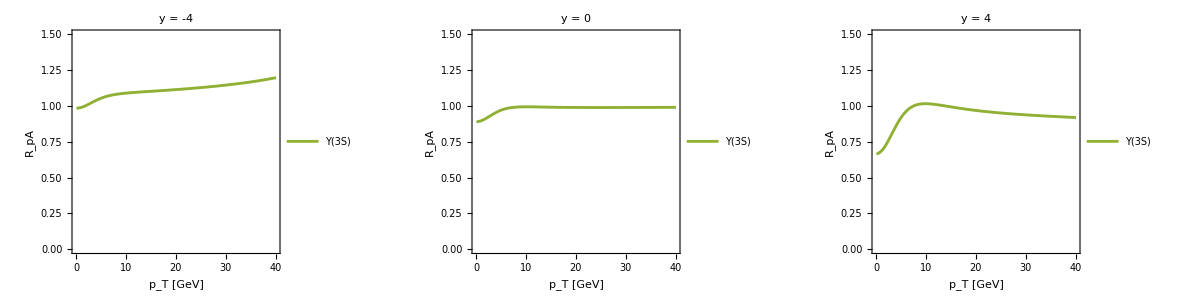

```mathematica
plot5= Grid[{{mypA3SPlotY[0.5],mypA3SPlotY[5],mypA3SPlotY[10]}}]
plot6 = Grid[{{mypA3SPlotPT[-4],mypA3SPlotPT[0],mypA3SPlotPT[4]}}]
```

## Read RpA data J/Psi

```mathematica
RpAJPsiresult=Interpolation[Import[wd<>"/../output_JPsi/RpA.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic]
RpAJPsierror=Interpolation[Import[wd<>"/../output_JPsi/RpA.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic]
{ymin,ymax} =RpAJPsiresult[[1,1]];
{ptmin,ptmax} =RpAJPsiresult[[1,2]];
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
Plot3D[RpAJPsiresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->{0,1.5}]
```

-Graphics3D-

```mathematica
(*Plot3D[RpAerror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->Automatic]*)
```

```mathematica
RpAJPsiresultU[y_,pt_]=RpAJPsiresult[y,pt]+RpAJPsierror[y,pt];
RpAJPsiresultL[y_,pt_]=RpAJPsiresult[y,pt]-RpAJPsierror[y,pt];
```

```mathematica
mypAJPsiPlotY[pt_]:=Plot[{RpAJPsiresult[y,pt],RpAJPsiresultL[y,pt],RpAJPsiresultU[y,pt]},{y,ymin,ymax},PlotStyle->{plotColor4,{Opacity[0.1],plotColor4},{Opacity[0.1],plotColor4}},Filling->{2->{3}},PlotLabel->Style["p_T = "<>ToString[pt]<>" GeV",18],FrameLabel->{"y","R_pA"},ImageSize->400,PlotRange->{0,1.5},PlotLegends->Placed[{"J/ψ"},{Right,Bottom}]]
mypAJPsiPlotPT[y_]:=Plot[{RpAJPsiresult[y,pt],RpAJPsiresultL[y,pt],RpAJPsiresultU[y,pt]},{pt,ptmin,ptmax},PlotStyle->{plotColor4,{Opacity[0.1],plotColor4},{Opacity[0.1],plotColor4}},Filling->{2->{3}},PlotLabel->Style["y = "<>ToString[y],18],FrameLabel->{"p_T [GeV]","R_pA"},ImageSize->400,PlotRange->{0,1.5},PlotLegends->Placed[{"J/ψ"},{Right,Bottom}]]
```

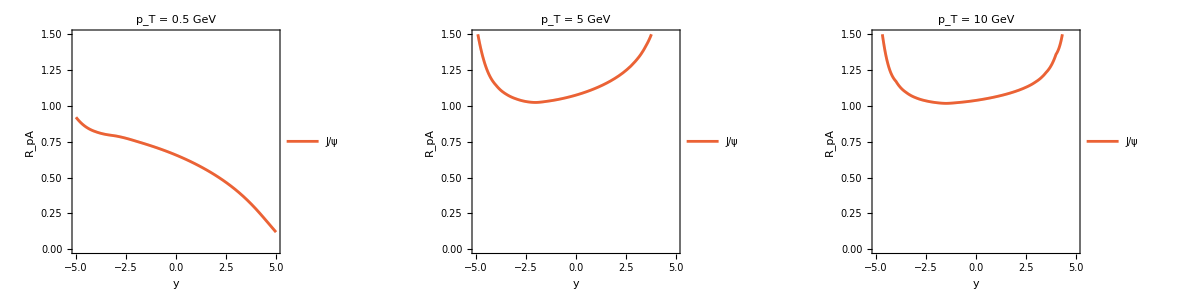

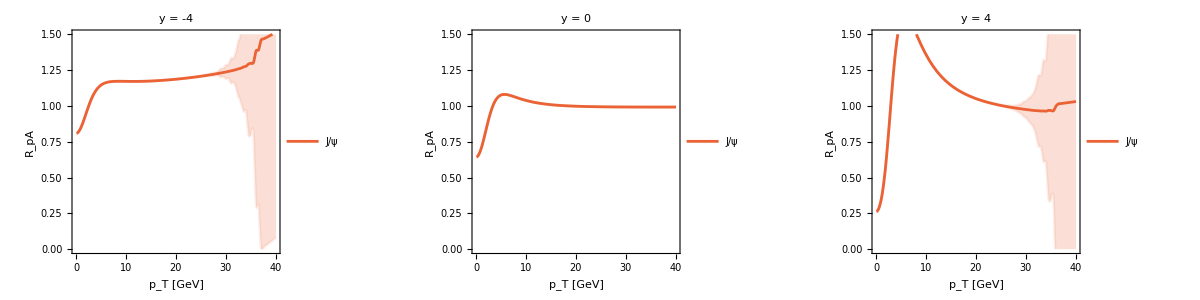

```mathematica
plot7 =Grid[{{mypAJPsiPlotY[0.5],mypAJPsiPlotY[5],mypAJPsiPlotY[10]}}]
plot8 = Grid[{{mypAJPsiPlotPT[-4],mypAJPsiPlotPT[0],mypAJPsiPlotPT[4]}}]
```

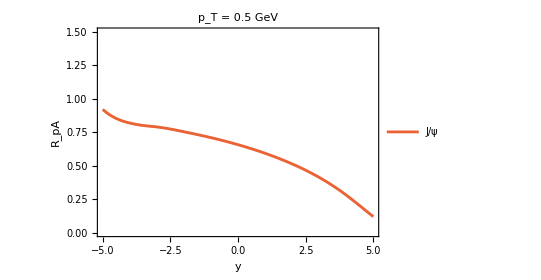

```mathematica
mypAJPsiPlotY[0.5]
```

## Compare: Υ(1S), Υ(2S), Υ(3S), J/Psi

```mathematica
Show[mypAYPlotY[0.5],mypA1SPlotY[0.5],mypA2SPlotY[0.5],mypA3SPlotY[0.5](*,mypAJPsiPlotY[0.5]*)]
Show[mypAYPlotY[5],mypA1SPlotY[5],mypA2SPlotY[5],mypA3SPlotY[5](*,mypAJPsiPlotY[5]*)]
Show[mypAYPlotY[10],mypA1SPlotY[10],mypA2SPlotY[10],mypA3SPlotY[10](*,mypAJPsiPlotY[10]*)]
```

```mathematica
Show[mypAYPlotPT[-4],mypA1SPlotPT[-4],mypA2SPlotPT[-4],mypA3SPlotPT[-4](*,mypAJPsiPlotPT[-4]*)]
Show[mypAYPlotPT[-2],mypA1SPlotPT[-2],mypA2SPlotPT[-2],mypA3SPlotPT[-2](*,mypAJPsiPlotPT[-2]*)]
Show[mypAYPlotPT[0],mypA1SPlotPT[0],mypA2SPlotPT[0],mypA3SPlotPT[0](*,mypAJPsiPlotPT[0]*)]
Show[mypAYPlotPT[2],mypA1SPlotPT[2],mypA2SPlotPT[2],mypA3SPlotPT[2](*,mypAJPsiPlotPT[2]*)]
Show[mypAYPlotPT[4],mypA1SPlotPT[4],mypA2SPlotPT[4],mypA3SPlotPT[4](*,mypAJPsiPlotPT[4]*)]
```

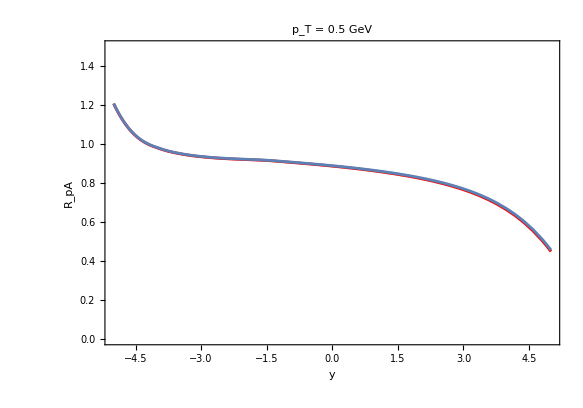

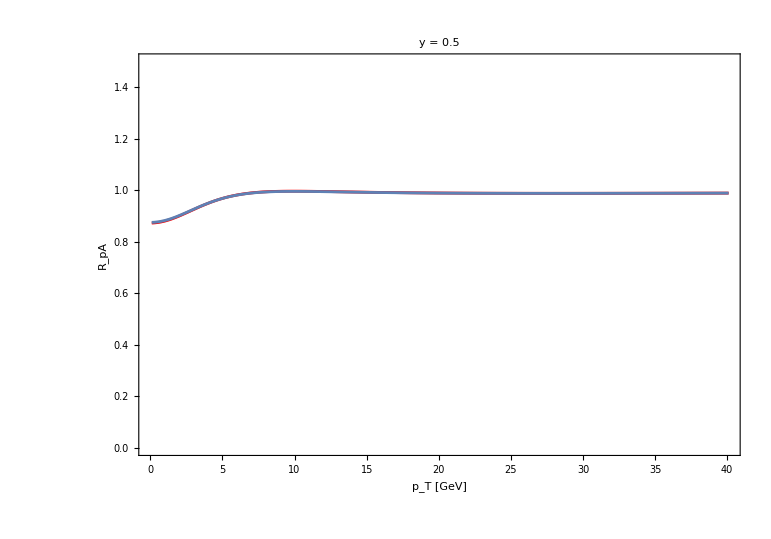

```mathematica
Show[mypAYPlotY[0.5],mypA1SPlotY[0.5]]
Show[mypAYPlotPT[0.5],mypA1SPlotPT[0.5]]
```